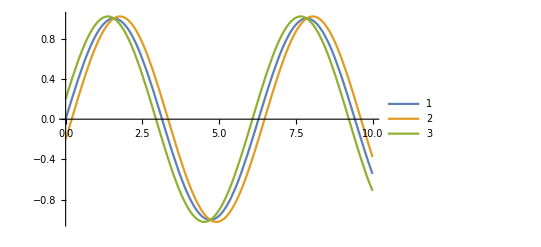

```mathematica
Plot[{Sin[t],Sin[t]-0.2Cos[t],Sin[t]+0.2Cos[t]},{t,0,10},PlotLegends->Automatic]
```

... the above plot is just to show that if the “strong” sine has a different sign than the “weak” cosine, then the presence of the weak cosine implies a weak “delay” or “lag” with respect to the pure strong sine signal.

Remark: for explicit evaluations, everything is measured in SI units. (Not the best choice, but at least quick.)

## Number of excited states: N = 1.

### Symbolic calculation => express C and R with equilibrium parameters (including derivatives of rates wrt energy splitting)

number of excited states: N = 1
energy gap fluctuates only (charge of ground state does not fluctuate, it’s zero. charge of excited state is also fixed, it’s one)

```mathematica
Solution=Solve[{
-c ω==ν Γd′(1-Pg0)-Γd0 s - Γu0 s-ν Γu′ Pg0,
s ω == -Γd0 c-Γu0 c
},{s,c}][[1]]
```

{s→-((Γd0+Γu0) (-Γd′ ν+Pg0 Γd′ ν+Pg0 Γu′ ν))/(Γd0^2+2 Γd0 Γu0+Γu0^2+ω^2),c→((-Γd′ ν+Pg0 Γd′ ν+Pg0 Γu′ ν) ω)/(Γd0^2+2 Γd0 Γu0+Γu0^2+ω^2)}

Assume δ(t) = δ0 + d sin(ω t), d >0.

```mathematica
sSol=s/.Solution
```

-((Γd0+Γu0) (-Γd′ ν+Pg0 Γd′ ν+Pg0 Γu′ ν))/(Γd0^2+2 Γd0 Γu0+Γu0^2+ω^2)

```mathematica
cSol=c/.Solution
```

((-Γd′ ν+Pg0 Γd′ ν+Pg0 Γu′ ν) ω)/(Γd0^2+2 Γd0 Γu0+Γu0^2+ω^2)

### What is the sign of sSol and cSol?

```mathematica
Quantity["BoltzmannConstant"]//UnitConvert
```

1.3806×10^-23 kg m^2/(s^2 K)

```mathematica
Quantity["PlanckConstant"]//UnitConvert
```

6.62607×10^-34 kg m^2/s

Note below the choice Γ >> ω this ensures “instantaneous thermalization”, implying that the “lag” or “delay” should be small, hence the resistance should be large.
Note also kB*T ≈ δ0. This ensures the the repopulation due to the drive (i.e., the δ0 oscillations) is significant.

```mathematica
Parameters={ω->2π*500*10^6,δ0->15*(10^-6)*1.6*(10^-19),T->0.2,kB->1.4*10^-23,e->1.6*10^-19,Γ->10^10,h->6.62*10^-34}
```

{ω→1000000000 π,δ0→2.4×10^-24,T→0.2,kB→1.4×10^-23,e→1.6×10^-19,Γ→10000000000,h→6.62×10^-34}

```mathematica
sSol/.Pg0->Γd0/(Γd0+Γu0)/.
{Γd0->Γ (1+n0),Γu0->Γ n0}/.
n0->1/(Exp[δ0/(kB T)]+1)/.
Γd′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)/.
Γu′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)//Simplify
```

(ⅇ^(δ0/(kB T)) Γ^2 ν)/(kB T ((3+ⅇ^(δ0/(kB T)))^2 Γ^2+(1+ⅇ^(δ0/(kB T)))^2 ω^2))

```mathematica
%/.Parameters
```

2.8238×10^22 ν

... it is positive.

```mathematica
cSol/.Pg0->Γd0/(Γd0+Γu0)/.
{Γd0->Γ (1+n0),Γu0->Γ n0}/.
n0->1/(Exp[δ0/(kB T)]+1)/.
Γd′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)/.
Γu′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)//Simplify
```

-(ⅇ^(δ0/(kB T)) (1+ⅇ^(δ0/(kB T))) Γ ν ω)/((3+ⅇ^(δ0/(kB T))) kB T ((3+ⅇ^(δ0/(kB T)))^2 Γ^2+(1+ⅇ^(δ0/(kB T)))^2 ω^2))

```mathematica
%/.Parameters
```

-5.55885×10^21 ν

... it is negative

### Derive Cq, Ctun, Rsis for ϵ0>0.

```mathematica
capacitance=e^2sSol/ν
```

-(e^2 (Γd0+Γu0) (-Γd′ ν+Pg0 Γd′ ν+Pg0 Γu′ ν))/(ν (Γd0^2+2 Γd0 Γu0+Γu0^2+ω^2))

```mathematica
inverseresistance=-e^2cSol ω/ν
```

-(e^2 (-Γd′ ν+Pg0 Γd′ ν+Pg0 Γu′ ν) ω^2)/(ν (Γd0^2+2 Γd0 Γu0+Γu0^2+ω^2))

```mathematica
capacitance/.Pg0->Γd0/(Γd0+Γu0)/.
{Γd0->Γ (1+n0),Γu0->Γ n0}/.
n0->1/(Exp[δ0/(kB T)]+1)/.
Γd′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)/.
Γu′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)//Simplify
```

(e^2 ⅇ^(δ0/(kB T)) Γ^2)/(kB T ((3+ⅇ^(δ0/(kB T)))^2 Γ^2+(1+ⅇ^(δ0/(kB T)))^2 ω^2))

```mathematica
%/.Parameters
```

7.22892×10^-16

... this is positive, approximately 0.7 fF.

```mathematica
inverseresistance/.Pg0->Γd0/(Γd0+Γu0)/.
{Γd0->Γ (1+n0),Γu0->Γ n0}/.
n0->1/(Exp[δ0/(kB T)]+1)/.
Γd′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)/.
Γu′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)//Simplify
```

(e^2 ⅇ^(δ0/(kB T)) (1+ⅇ^(δ0/(kB T))) Γ ω^2)/((3+ⅇ^(δ0/(kB T))) kB T ((3+ⅇ^(δ0/(kB T)))^2 Γ^2+(1+ⅇ^(δ0/(kB T)))^2 ω^2))

```mathematica
%/.Parameters
```

4.47069×10^-7

...this is positive. Converting to resistance:

```mathematica
1/%
```

2.23679×10^6

... approximately 2.23 MOhm.

Contrast resistance to Zoli’s result:

```mathematica
invresZoli=e^2(-1)λ^2η ω^2/(ω^2+γ^2)//.{λ->1,γ->Γ Coth[δ0/(2 kB T)],η->γ/(4 kB T Cosh[δ0/(2kB T)]^2)}
%/.Parameters
```

-(e^2 Γ ω^2 Csch[δ0/(2 kB T)] Sech[δ0/(2 kB T)])/(4 kB T (ω^2+Γ^2 Coth[δ0/(2 kB T)]^2))

-7.5068×10^-7

```mathematica
1/%
```

-1.33213×10^6

from Esterli:

```mathematica
invresEsterli=(4RQ kB T /(h γ))((ω^2+γ^2)/ω^2)Cosh[δ0/(2kB T)]^2
```

(4 kB RQ T (γ^2+ω^2) Cosh[δ0/(2 kB T)]^2)/(h γ ω^2)

```mathematica
%/.RQ->h/(e^2)
```

(4 kB T (γ^2+ω^2) Cosh[δ0/(2 kB T)]^2)/(e^2 γ ω^2)

```mathematica
%/.γ->Γ Coth[δ0/(2 kB T)]
```

(4 kB T Cosh[δ0/(2 kB T)] (ω^2+Γ^2 Coth[δ0/(2 kB T)]^2) Sinh[δ0/(2 kB T)])/(e^2 Γ ω^2)

```mathematica
%/.Parameters
```

1.33213×10^6

### Check tun capacitance Zoli vs. Esterli

Esterli

```mathematica
CtunEsterli=(e^2/2)(1/(2kB T))(γ^2/(γ^2+ω^2))/Cosh[δ0/(2kB T)]^2
```

(e^2 γ^2 Sech[δ0/(2 kB T)]^2)/(4 kB T (γ^2+ω^2))

```mathematica
%/.γ->Γ Coth[δ0/(2 kB T)]/.Parameters
```

1.88208×10^-15

Zoli

```mathematica
CtunZoli=-e^2λ^2 η γ/(ω^2+γ^2)
```

-(e^2 γ η λ^2)/(γ^2+ω^2)

```mathematica
%//.{λ->1,γ->Γ Coth[δ0/(2 kB T)],η->γ/(4 kB T Cosh[δ0/(2kB T)]^2)}
```

-(e^2 Γ^2 Csch[δ0/(2 kB T)]^2)/(4 kB T (ω^2+Γ^2 Coth[δ0/(2 kB T)]^2))

```mathematica
%/.Parameters
```

-1.88208×10^-15

### Derive Cq, Ctun, Rs with `primary parameters’ (e.g., temperature)!

```mathematica
sBasic=s/.Solution/.Pg0->Γd0/(Γd0+Γu0)/.
{Γd0->Γ (1+n0),Γu0->Γ n0}/.
n0->1/(Exp[δ0/(kB T)]+1)/.
Γd′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)/.
Γu′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)//Simplify
```

(ⅇ^(δ0/(kB T)) Γ^2 ν)/(kB T ((3+ⅇ^(δ0/(kB T)))^2 Γ^2+(1+ⅇ^(δ0/(kB T)))^2 ω^2))

### Evaluations, plots.

```mathematica
Quantity["BoltzmannConstant"]//UnitConvert
```

1.3806×10^-23 kg m^2/(s^2 K)

```mathematica
Parameters={ω->2π*500*10^6,δ0->15*10^-6*1.6*10^-19,T->0.1,kB->1.4*10^-23,e->1.6*10^-19}
```

{ω→1000000000 π,δ0→2.4×10^-24,T→0.1,kB→1.4×10^-23,e→1.6×10^-19}

```mathematica
sBasic/.Parameters
```

(3.96622×10^24 Γ^2 ν)/(4.23781×10^20+73.1488 Γ^2)

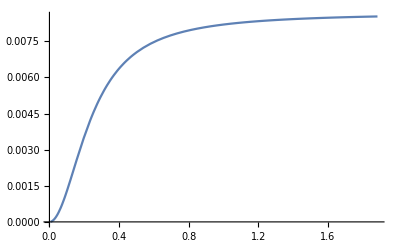

```mathematica
Plot[sBasic/(ν/(1.6*10^-25))/.Parameters,{Γ,2π*10*10^6,2π*3000*10^6}]
```

Plot it as a capacitance (assume ng = 1)

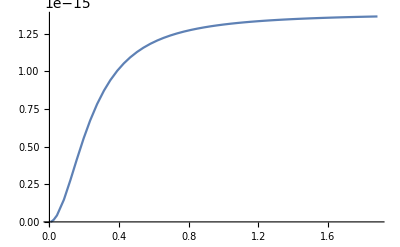

```mathematica
Plot[sBasic*e/(ν/e)//.Parameters,{Γ,2π*10*10^6,2π*3000*10^6}]
```

```mathematica
cBasic=c/.Solution/.Pg0->Γd0/(Γd0+Γu0)/.
{Γd0->Γ (1+n0),Γu0->Γ n0}/.
n0->1/(Exp[δ0/(kB T)]+1)/.
Γd′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)/.
Γu′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)//Simplify
```

-(ⅇ^(δ0/(kB T)) (1+ⅇ^(δ0/(kB T))) Γ ν ω)/((3+ⅇ^(δ0/(kB T))) kB T ((3+ⅇ^(δ0/(kB T)))^2 Γ^2+(1+ⅇ^(δ0/(kB T)))^2 ω^2))

```mathematica
cBasic/.Parameters
```

-(9.54649×10^33 Γ ν)/(4.23781×10^20+73.1488 Γ^2)

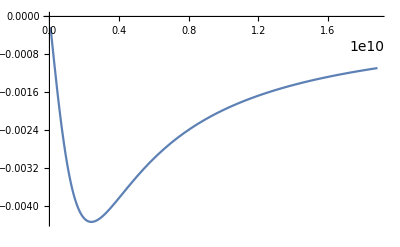

```mathematica
Plot[cBasic/(ν/(1.6*10^-25))/.Parameters,{Γ,2π*10*10^6,2π*3000*10^6}]
```

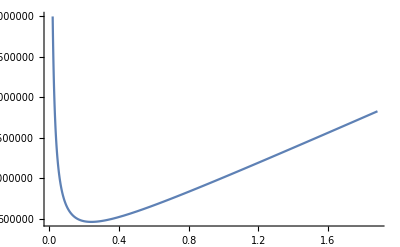

```mathematica
Plot[-(ν/e)/(cBasic e ω)/.Parameters,{Γ,2π*10*10^6,2π*3000*10^6}]
```

## Zoli & Rupesh results with N > 1

Assume ϵ >ϵt, with ϵt being the touching point

```mathematica
capZoliN=-(ng0-ne0)e^2λ^2η γ δ′/(ω^2+γ^2)
```

(e^2 (ne0-ng0) γ δ′ η λ^2)/(γ^2+ω^2)

```mathematica
invresZoliN=-(ng0-ne0)e^2λ^2η ω^2δ′/(ω^2+γ^2)
```

(e^2 (ne0-ng0) δ′ η λ^2 ω^2)/(γ^2+ω^2)

```mathematica
capZoliN/.{ng0->0,ne0->1}/.δ′->1
```

(e^2 γ η λ^2)/(γ^2+ω^2)

```mathematica
invresZoliN/.{ng0->0,ne0->1}/.δ′->1
```

(e^2 η λ^2 ω^2)/(γ^2+ω^2)

```mathematica
Symbols={
λ->(Exp[δ0/(kB T)]+1)/(Exp[δ0/(kB T)]+Ν),
γ->Γ(Exp[δ0/(kB T)]+Ν)/(Exp[δ0/(kB T)]-1),
η-> Ν γ/(4 kB T Cosh[δ0/(2kB T)]^2)
}
```

{λ→(1+ⅇ^(δ0/(kB T)))/(ⅇ^(δ0/(kB T))+Ν),γ→(Γ (ⅇ^(δ0/(kB T))+Ν))/(-1+ⅇ^(δ0/(kB T))),η→(γ Ν Sech[δ0/(2 kB T)]^2)/(4 kB T)}

### tunneling capacitance

```mathematica
capZoliNPrimary=capZoliN/.{ng0->0,ne0->1}/.δ′->1//.Symbols
```

(e^2 (1+ⅇ^(δ0/(kB T)))^2 Γ^2 Ν Sech[δ0/(2 kB T)]^2)/(4 (-1+ⅇ^(δ0/(kB T)))^2 kB T ((Γ^2 (ⅇ^(δ0/(kB T))+Ν)^2)/((-1+ⅇ^(δ0/(kB T)))^2)+ω^2))

```mathematica
capZoliNPrimary/.Parameters/.Ν->1
```

1.88208×10^-15

```mathematica
capZoliNPrimary/.Parameters/.Ν->10^3
```

2.14432×10^-17

```mathematica
capZoliNPrimary/.Parameters/.Ν->10^10
```

2.15444×10^-24

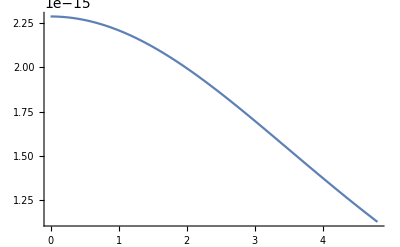

```mathematica
Plot[capZoliNPrimary/.δ0->ϵ/.Parameters/.Ν->1,{ϵ,0,30*10^-6*1.6*10^-19}]
```

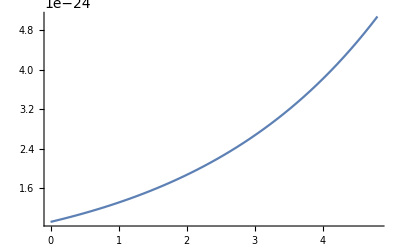

```mathematica
Plot[capZoliNPrimary/.δ0->ϵ/.Parameters/.Ν->10^10,{ϵ,0,30*10^-6*1.6*10^-19}]
```

### sisyphus resistance

```mathematica
invresZoliNPrimary=invresZoliN/.{ng0->0,ne0->1}/.δ′->1//.Symbols
```

(e^2 (1+ⅇ^(δ0/(kB T)))^2 Γ Ν ω^2 Sech[δ0/(2 kB T)]^2)/(4 (-1+ⅇ^(δ0/(kB T))) kB T (ⅇ^(δ0/(kB T))+Ν) ((Γ^2 (ⅇ^(δ0/(kB T))+Ν)^2)/((-1+ⅇ^(δ0/(kB T)))^2)+ω^2))

```mathematica
invresZoliNPrimary/.Ν->1/.Parameters
1/%
```

7.5068×10^-7

1.33213×10^6

... that is, the resistance is 1.3 MOhm, which is roughly 1/(0.01 G0) with G0 = 2e^2/h.

```mathematica
invresZoliNPrimary/.Parameters/.Ν->10^3
```

2.86392×10^-11

```mathematica
invresZoliNPrimary/.Parameters/.Ν->10^10
```

2.88422×10^-25

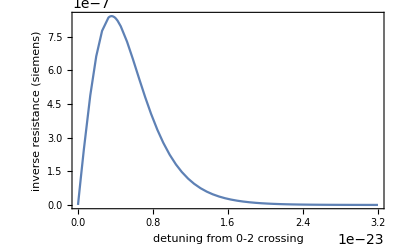

```mathematica
Plot[invresZoliNPrimary/.δ0->ϵ/.Parameters/.Ν->1,{ϵ,0,200*10^-6*1.6*10^-19},FrameLabel->{"detuning from 0-2 crossing","inverse resistance (siemens)" },Axes->False,Frame->True]
```

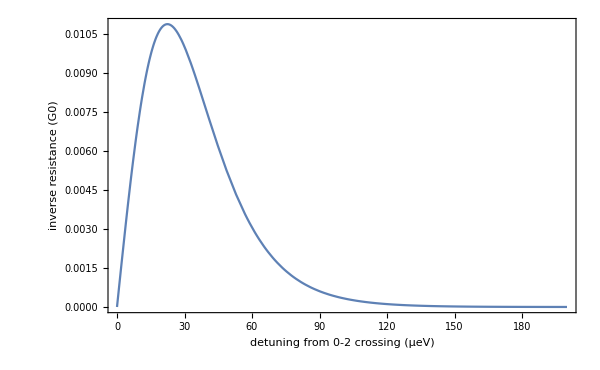

```mathematica
Plot[invresZoliNPrimary/(2e^2/h)/.δ0->ϵ*10^-6*1.6*10^-19/.Parameters/.Ν->1,{ϵ,0,200},FrameLabel->{"detuning from 0-2 crossing (μeV)","inverse resistance (G0)" },Axes->False,Frame->True,FrameStyle->Large,ImageSize->600]
```

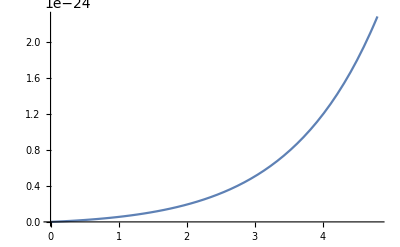

```mathematica
Plot[invresZoliNPrimary/.δ0->ϵ/.Parameters/.Ν->10^10,{ϵ,0,30*10^-6*1.6*10^-19}]
```

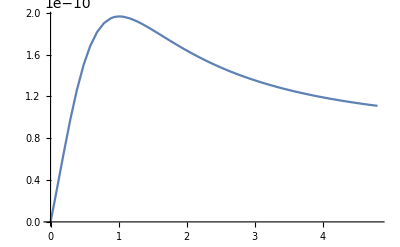

```mathematica
Plot[invresZoliNPrimary/.δ0->ϵ/.Γ->10^4/.Parameters/.Ν->10^5,{ϵ,0,30*10^-6*1.6*10^-19},PlotRange->Full]
```

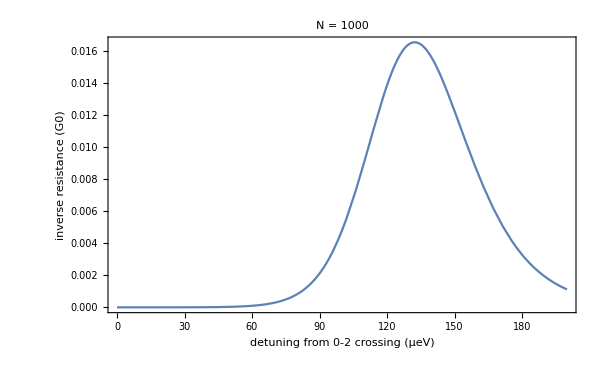

```mathematica
Plot[invresZoliNPrimary/(2e^2/h)/.δ0->ϵ*10^-6*1.6*10^-19/.Parameters/.Ν->1000,{ϵ,0,200},FrameLabel->{"detuning from 0-2 crossing (μeV)","inverse resistance (G0)" },Axes->False,Frame->True,FrameStyle->Large,ImageSize->600,PlotLabel->"N = 1000"]
```

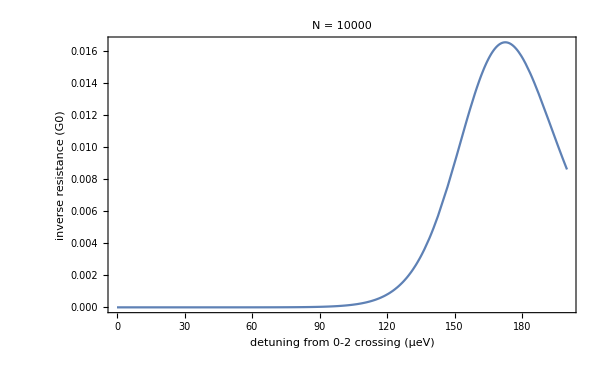

```mathematica
Plot[invresZoliNPrimary/(2e^2/h)/.δ0->ϵ*10^-6*1.6*10^-19/.Parameters/.Ν->10000,{ϵ,0,200},FrameLabel->{"detuning from 0-2 crossing (μeV)","inverse resistance (G0)" },Axes->False,Frame->True,FrameStyle->Large,ImageSize->600,PlotLabel->"N = 10000"]
```

## Number of excited states N>1

```mathematica
Solution=Solve[{
-c ω==ν Γd′(1-Pg0)-Γd0 s - Ν Γu0 s-ν Ν Γu′ Pg0,
s ω == -Γd0 c-Ν Γu0 c
},{s,c}][[1]]
```

{s→-((Γd0+Γu0 Ν) (-Γd′ ν+Pg0 Γd′ ν+Pg0 Γu′ ν Ν))/(Γd0^2+2 Γd0 Γu0 Ν+Γu0^2 Ν^2+ω^2),c→((-Γd′ ν+Pg0 Γd′ ν+Pg0 Γu′ ν Ν) ω)/(Γd0^2+2 Γd0 Γu0 Ν+Γu0^2 Ν^2+ω^2)}

```mathematica
sBasic=s/.Solution/.Pg0->Γd0/(Γd0+Ν Γu0)/.
{Γd0->Γ (1+n0),Γu0->Γ n0}/.
n0->1/(Exp[δ0/(kB T)]+1)/.
Γd′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)/.
Γu′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)//Simplify
```

(ⅇ^(δ0/(kB T)) Γ^2 ν Ν)/(kB T (Γ^2 (2+ⅇ^(δ0/(kB T))+Ν)^2+(1+ⅇ^(δ0/(kB T)))^2 ω^2))

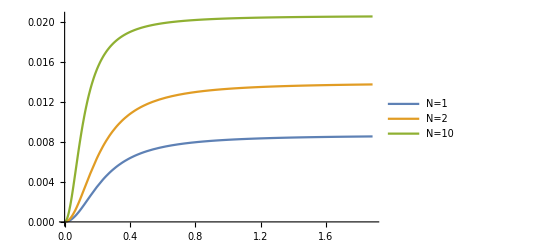

```mathematica
Plot[{
sBasic/(ν/(1.6*10^-25))/.Ν->1/.Parameters,
sBasic/(ν/(1.6*10^-25))/.Ν->2/.Parameters,
sBasic/(ν/(1.6*10^-25))/.Ν->10/.Parameters
},{Γ,2π*10*10^6,2π*3000*10^6},PlotLegends->{"N=1","N=2","N=10"}]
```

Plot as capacitance:

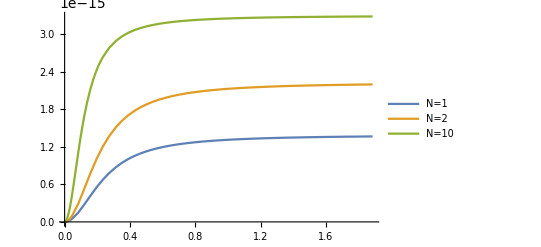

```mathematica
Plot[{
sBasic*e/(ν/e)/.Ν->1/.Parameters,
sBasic*e/(ν/e)/.Ν->2/.Parameters,
sBasic*e/(ν/e)/.Ν->10/.Parameters
},{Γ,2π*10*10^6,2π*3000*10^6},PlotLegends->{"N=1","N=2","N=10"}]
```

```mathematica
cBasic=c/.Solution/.Pg0->Γd0/(Γd0+Ν Γu0)/.
{Γd0->Γ (1+n0),Γu0->Γ n0}/.
n0->1/(Exp[δ0/(kB T)]+1)/.
Γd′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)/.
Γu′->Γ (D[1/(Exp[(δ0+d)/(kB T)]+1),d]/.d->0)//Simplify
```

-(ⅇ^(δ0/(kB T)) (1+ⅇ^(δ0/(kB T))) Γ ν Ν ω)/(kB T (2+ⅇ^(δ0/(kB T))+Ν) (Γ^2 (2+ⅇ^(δ0/(kB T))+Ν)^2+(1+ⅇ^(δ0/(kB T)))^2 ω^2))

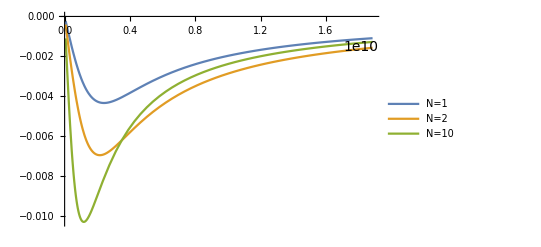

```mathematica
Plot[{
cBasic/(ν/(1.6*10^-25))/.Ν->1/.Parameters,
cBasic/(ν/(1.6*10^-25))/.Ν->2/.Parameters,
cBasic/(ν/(1.6*10^-25))/.Ν->10/.Parameters
},{Γ,2π*10*10^6,2π*3000*10^6},PlotLegends->{"N=1","N=2","N=10"}]
```

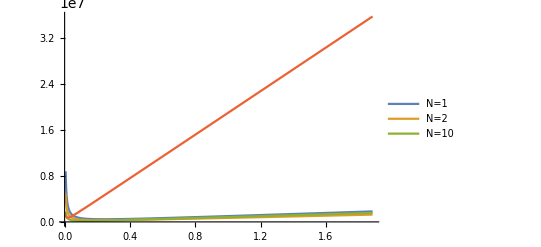

```mathematica
Plot[{
-(ν/e)/(cBasic e ω)/.Ν->1/.Parameters,
-(ν/e)/(cBasic e ω)/.Ν->2/.Parameters,
-(ν/e)/(cBasic e ω)/.Ν->10/.Parameters,
-(ν/e)/(cBasic e ω)/.Ν->100/.Parameters,
},{Γ,2π*10*10^6,2π*3000*10^6},PlotLegends->{"N=1","N=2","N=10"}]
```

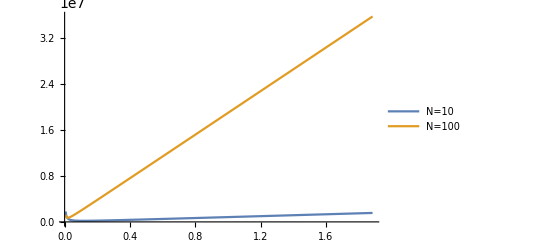

```mathematica
Plot[{
-(ν/e)/(cBasic e ω)/.Ν->10/.Parameters,
-(ν/e)/(cBasic e ω)/.Ν->100/.Parameters
},{Γ,2π*10*10^6,2π*3000*10^6},PlotLegends->{"N=10","N=100"}]
```